```mathematica
Exit[]
```

```mathematica
<<Notation`
Symbolize[Subscript[x_, y_]];
```

```mathematica
ℐ = IdentityMatrix[3];
F = {{Subscript[λ, 1],0,0},{0,Subscript[λ, 2],0},{0,0,Subscript[λ, 3]}}/.Subscript[λ, 2]->Subscript[λ, 1]
Β= F.Transpose[F]
J = Assuming[{Subscript[λ, 1]>0,Subscript[λ, 2]>0,Subscript[λ, 3]>0},Simplify@Det[F]]
EL=1/2(Transpose[F].F-ℐ);
Diagonal[EL]
```

{{λ_1,0,0},{0,λ_1,0},{0,0,λ_3}}

{{λ_1^2,0,0},{0,λ_1^2,0},{0,0,λ_3^2}}

λ_1^2 λ_3

{1/2 (-1+λ_1^2),1/2 (-1+λ_1^2),1/2 (-1+λ_3^2)}

```mathematica
(Compressible[0#,5 #,0.2]-1)*10&/@Range[0,1,0.2]//TableForm
```

0. | 0.
-0.219526 | 1.10966
-0.475646 | 2.48201
-0.762804 | 4.19215
-1.07224 | 6.3241
-1.39212 | 8.96039

```mathematica
(Compressible[1#,3#,5#,0.2]-1)*10&/@Range[0,1,0.2]//TableForm
```

0. | 0. | 0.
-0.205175 | 0.334949 | 0.902346
-0.574812 | 0.642232 | 1.98532
-1.11348 | 0.960726 | 3.35106
-1.8371 | 1.35717 | 5.13727
-2.7644 | 1.96547 | 7.52298

```mathematica
C10
D1
```

2.08333

0.36

```mathematica
Compressible[Subscript[p, 1]:_,Subscript[p, 2]:_,Subscript[p, 3]:_,ν_]:=Block[{Ε=10,ℐ,F,Β,J,Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3],Subscript[μ, 1],Κ,σ,p,Sol,tol=10^-6},
ℐ = IdentityMatrix[3];
F = {{Subscript[λ, 1],0,0},{0,Subscript[λ, 2],0},{0,0,Subscript[λ, 3]}}(*/.Subscript[λ, 2]->Subscript[λ, 1]*);
Β= F.Transpose[F];
J = Simplify@Det[F];
Subscript[μ, 1]=Ε/(2(1+ν));
Κ=Ε/(3(1-2ν));
σ =Subscript[μ, 1]/J^(5/3)(Β-1/3 Tr[Β]ℐ)+Κ (J-1)ℐ;
Sol=NSolve[σ[[1,1]] J/Subscript[λ, 1]==Subscript[p, 1]&&σ[[2,2]] J/Subscript[λ, 2]==Subscript[p, 2]&&σ[[3,3]] J/Subscript[λ, 3]==Subscript[p, 3]&&Subscript[λ, 1]>0&&Subscript[λ, 2]>0&&Subscript[λ, 3]>0,{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]},Reals];
If[(Sol==={})||(Abs[(σ[[1,1]] J/Subscript[λ, 1]/.Sol[[1]])-Subscript[p, 1]]>tol)||(Abs[(σ[[2,2]] J/Subscript[λ, 2]/.Sol[[1]])-Subscript[p, 2]]>tol)||(Abs[(σ[[3,3]] J/Subscript[λ, 3]/.Sol[[1]])-Subscript[p, 3]]>tol),Null
(*,MaximalBy[{Log[Subscript[λ, 1]],Log[Subscript[λ, 3]]}/.Sol[[1]],Abs][[1]]*)
(*,1/2((Max[{Subscript[λ, 1],Subscript[λ, 3]}/.Sol[[1]]])^2-1)*)
,{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}/.Sol[[1]]
]
]
InCompressible[Subscript[p, 1]:_,Subscript[p, 3]:_]:=Block[{Ε=1,ν=0.5,ℐ,F,Β,J,Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3],Subscript[μ, 1],Κ,σ,p,Sol,tol=10^-6},
ℐ = IdentityMatrix[3];
F = {{Subscript[λ, 1],0,0},{0,Subscript[λ, 2],0},{0,0,Subscript[λ, 3]}}/.Subscript[λ, 2]->Subscript[λ, 1];
Β= F.Transpose[F];
J = Simplify@Det[F];
Subscript[μ, 1]=Ε/(2(1+ν));
σ = Subscript[μ, 1](Β-1/3 Tr[Β]ℐ)+p/3 ℐ;
Sol=NSolve[σ[[1,1]]==Subscript[p, 1]&&σ[[3,3]]==Subscript[p, 3]&&J==1&&Subscript[λ, 1]>0&&Subscript[λ, 3]>0,{Subscript[λ, 1],Subscript[λ, 3],p},Reals];
If[(Sol==={})||(Abs[(σ[[1,1]]/.Sol[[1]])-Subscript[p, 1]]>tol)||(Abs[(σ[[3,3]]/.Sol[[1]])-Subscript[p, 3]]>tol)||(Abs[(J/.Sol[[1]])-1]>tol),Null
(*,MaximalBy[{Log[Subscript[λ, 1]],Log[Subscript[λ, 3]]}/.Sol[[1]],Abs][[1]]*)
,{Subscript[λ, 1],Subscript[λ, 3]}/.Sol[[1]]
]
]
StrainMeasure[Null]=Null
StrainMeasure[{Subscript[λ, 1]:_,Subscript[λ, 3]:_}]:=Block[{},
(*MaximalBy[{Log[Subscript[λ, 1]],Log[Subscript[λ, 3]]},Abs][[1]]*)
(*1/2(Max[{Subscript[λ, 1],Subscript[λ, 3]}]^2-1)*)
Log[Subscript[λ, 1]]
]
```

```mathematica
ClearAll[InComp,Comp,CC,CCL]
InComp[α_,p10_,p1e_,n_]:=Block[{p30,p3e
,p1List,p3List,StrainList},
p30=α p10;
p3e=α p1e;
p1List = Subdivide[p10,p1e,n-1];
p3List = Subdivide[p30,p3e,n-1];
StrainList=MapThread[InCompressible[#1,#2]&,{p1List,p3List}];
StrainMeasure/@StrainList
]
Comp[ν_,α_,p10_,p1e_,n_]:=Block[{p30,p3e
,p1List,p3List,StrainList},
p30=α p10;
p3e=α p1e;
p1List = Subdivide[p10,p1e,n-1];
p3List = Subdivide[p30,p3e,n-1];
StrainList=MapThread[Compressible[#1,#2,ν]&,{p1List,p3List}];
StrainMeasure/@StrainList
]
CCL[ν_,α_,p1eL_]:=Block[{p10=0,n=100,p1List,CC1},
p1List = N/@Subdivide[p10,p1eL,n-1];
CC1= Comp[ν,α,p10,p1eL,n];
Transpose[{p1List,CC1}]]
CC[ν_,α_,p1eL_]:=Join[Block[{p10=0,n=100,p1List,CC1},
p1List = N/@Subdivide[p10,p1eL,n-1];
CC1= Comp[ν,α,p10,p1eL,n];
Transpose[{p1List,CC1}]],
Block[{p10=0,p1e=100,n=100,p1List,CC1},
p1List = N/@Subdivide[p10,p1e,n-1];
CC1= Comp[ν,α,p10,p1e,n];
Transpose[{p1List,CC1}]]
]
```

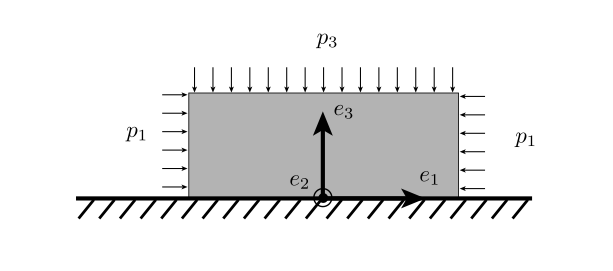

## p_3/p_1=1 (Hydrostatic)

```mathematica
Plt11 =With[{α=1,p10=-100,p1e=100,n=100},
ListLinePlot[InComp[α,p10,p1e,n],DataRange->{p10,p1e},
{PlotStyle->Directive[Red,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
Plt12=With[{ν=0.3,α=1},
ListLinePlot[CC[ν,α,-1],
{PlotStyle->Directive[Blue,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
Plt13=With[{ν=0.49,α=1},
ListLinePlot[CC[ν,α,-20],
{PlotStyle->Directive[Green,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
LL = LineLegend[{Red,Green,Blue},{"ν = 0.5","ν = 0.49","ν = 0.3"},LabelStyle->{Black,FontFamily->"Times",24},LegendMarkers->"●",LegendMarkerSize->30];
```

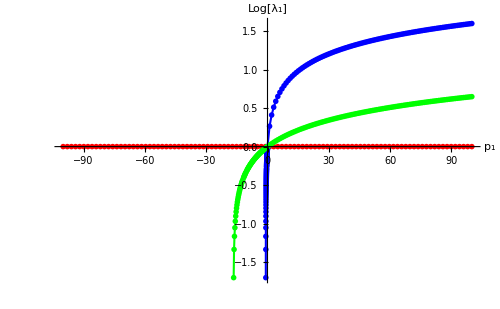

```mathematica
Row[{Show[{Plt11,Plt12,Plt13},PlotRange->All],LL}]
```

## p_3/p_1=0.99

```mathematica
Plt41 =With[{α=0.99,p10=-100,p1e=100,n=100},
ListLinePlot[InComp[α,p10,p1e,n],DataRange->{p10,p1e},
{PlotStyle->Directive[Red,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
Plt42=With[{ν=0.3,α=0.99},
ListLinePlot[CC[ν,α,-1],
{PlotStyle->Directive[Blue,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
Plt43=With[{ν=0.49,α=0.99},
ListLinePlot[CC[ν,α,-20],
{PlotStyle->Directive[Green,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
```

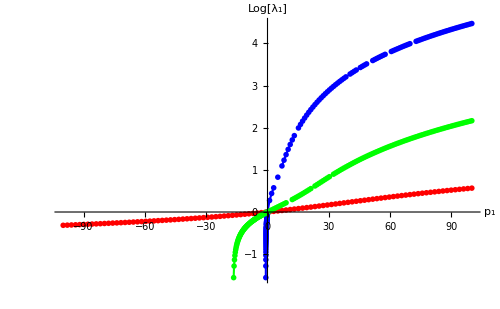

```mathematica
Row[{Show[{Plt41,Plt42,Plt43},PlotRange->All],LL}]
```

## p_3/p_1=0.9

```mathematica
Plt21 =With[{α=0.9,p10=-100,p1e=100,n=100},
ListLinePlot[InComp[α,p10,p1e,n],DataRange->{p10,p1e},
{PlotStyle->Directive[Red,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
Plt22=With[{ν=0.3,α=0.9},
ListLinePlot[CC[ν,α,-1],
{PlotStyle->Directive[Blue,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
Plt23=With[{ν=0.49,α=0.9},
ListLinePlot[CC[ν,α,-20],
{PlotStyle->Directive[Green,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
```

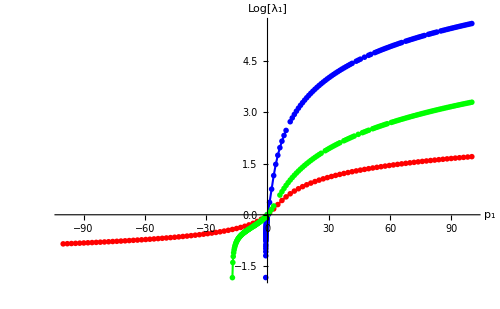

```mathematica
Row[{Show[{Plt21,Plt22,Plt23},PlotRange->All],LL}]
```

## p_3/p_1=0.5

```mathematica
Plt31 =With[{α=0.5,p10=-100,p1e=100,n=100},
ListLinePlot[InComp[α,p10,p1e,n],DataRange->{p10,p1e},
{PlotStyle->Directive[Red,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
Plt32=With[{ν=0.3,α=0.5},
ListLinePlot[CC[ν,α,-1],
{PlotStyle->Directive[Blue,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
Plt33=With[{ν=0.49,α=0.5},
ListLinePlot[CC[ν,α,-20],
{PlotStyle->Directive[Green,Thickness[0.003]],PlotMarkers->{Automatic,0.02}},
PlotRange->Automatic,ImageSize->500,GridLines->None,Axes->True,AxesStyle->Directive[Black,FontFamily->"Times",24],
AxesLabel->{Style["p_1",Black,FontFamily->"Times",24],Style["Log[λ_1]",Black,FontFamily->"Times",24]},RotateLabel->False]
];
```

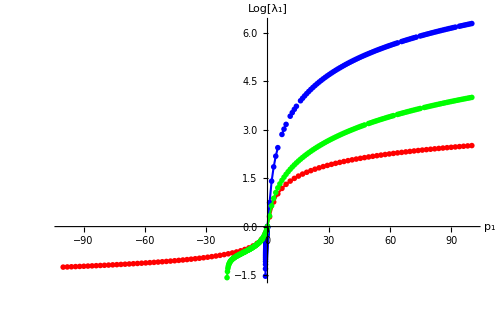

```mathematica
Row[{Show[{Plt31,Plt32,Plt33},PlotRange->All],LL}]
```